```mathematica
tank=Graphics3D[{
Table[{Blue,Sphere[{RandomReal[{-0.75,0.75}],RandomReal[{-0.75,0.75}],0.05},RandomReal[0.1]]},{20 n0f}],
Table[{Green,Sphere[{RandomReal[{-0.75,0.75}],RandomReal[{-0.75,0.75}],0.05},RandomReal[0.1]]},{20 n1f}],
{Opacity[0.55],Cylinder[{{0,0,0},{0,0,1.75}}]},
If[n2f≥0.05,{Opacity[0.35],RGBColor[1,0.968627,0],Cylinder[{{0,0,0},{0,0,1.5}}]}],
{Gray,Cylinder[{{0,0,1.5},{0,0,0.25+1.5}}]},
{Gray,Cylinder[{{0,0,1.5+0.25},{0,0,0.5+1.5}},0.15]},
If[n2f≥0.05,Text[Style[Subscript["CO","2"],18],{0,0,0.5*1.5}]]
},Boxed->False,ViewPoint->Front,Lighting->{{"Ambient",LightGray}},PlotRange->{{-1,1},{-1,1},{-0.4,2.55}},AspectRatio->Full,ImagePadding->{{Automatic,Automatic},{20,Automatic}},ImageSize->{245,300},ContentSelectable->False];

Graphics[{
Text[Row[{Style["●",25,Blue],Style[Row[{"= ",Subscript["CaCO","3"]}],15],Spacer[5],Style["●",25,Green],Style[Row[{"= ","CaO"}],15]}],{0,-0.65}],
Inset[tank,{0,0}]
}]
```

-Graphics-

```mathematica
Manipulate[
Module[{n0f,n1f,norm},
n0f=1.28;n1f=0.72;
(*norm=(n2f+min)/(max-min);*)
norm=n2f/2;
Graphics[{
Inset[
Graphics3D[{
Text[Style[norm,16],{0,0,2}],
Table[{RGBColor[0.0667,0.5032,1],Sphere[{RandomReal[{-0.75,0.75}],RandomReal[{-0.75,0.75}],0.05},RandomReal[0.1]]},{20 n0f}],
Table[{RGBColor[0.361,0.8,0],Sphere[{RandomReal[{-0.75,0.75}],RandomReal[{-0.75,0.75}],0.05},RandomReal[0.1]]},{20 n1f}],
(*{EdgeForm[{Thickness[0.01],Black}],If[n2f≤0.005,
{Opacity[0.55],Cylinder[{{0,0,0},{0,0,1.5}}]},
{Opacity[0.25],RGBColor[1,0.968627,0],Cylinder[{{0,0,0},{0,0,1.5}}]}
]
},*)

{EdgeForm[{Thickness[0.01],Black}],Opacity[0.36],Blend[{White,RGBColor[1,0.968627,0]},norm],Cylinder[{{0,0,0},{0,0,1.5}}]},
(*{EdgeForm[{Thickness[0.01],Black}],Opacity[0.55],Cylinder[{{0,0,0},{0,0,1.5}}]},*)

{Gray,Cylinder[{{0,0,1.5},{0,0,1.55}}]},
If[n2f≥0.05,Text[Style[Subscript["CO","2"],18],{0,0,0.5*1.5}]],
Text[Row[{Style["●",25,RGBColor[0.0667,0.5032,1]],Style[Row[{"= ",Subscript["CaCO","3"]}],15],Spacer[5],Style["●",25,RGBColor[0.361,0.8,0]],Style[Row[{"= ","CaO"}],15]}],{0,0,-0.5}]
},Boxed->False,ViewPoint->Front,Lighting->{{"Ambient",LightGray}},PlotRange->{{-1,1},{-1,1},{-0.4,2.55}},AspectRatio->Full,ImagePadding->{{Automatic,Automatic},{20,Automatic}},ImageSize->{245,300}],{0,0}]
},ImageSize->{245,300}]
],
{{n2f,0.72,""},0,2,0.01,Appearance->"Labeled"}(*,
{{min,0,"min"},-1,0,0.01,Appearance->"Labeled"},
{{max,2,"max"},2,3,0.01,Appearance->"Labeled"}*)]
```

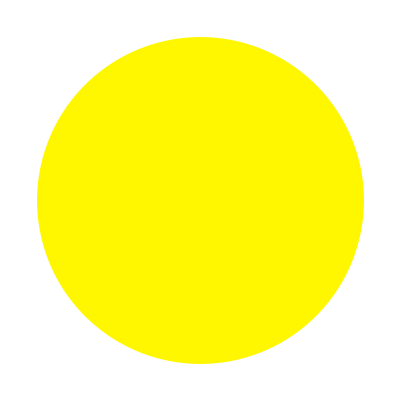
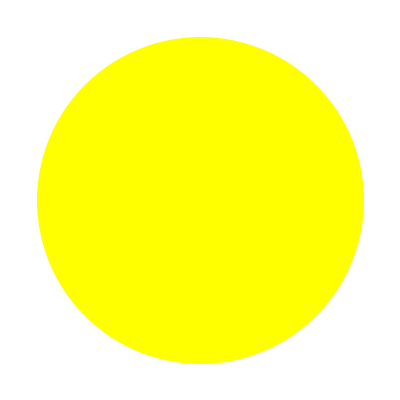
-Graphics3D- | -Graphics3D-
-Graphics- | -Graphics-

```mathematica
Grid[{
{Graphics3D[{RGBColor[1,0.968627,0],Cylinder[{{0,0,0},{0,0,1.5}}]},Lighting->{{"Ambient",LightGray}},ViewPoint->Front],
Graphics3D[{Yellow,Cylinder[{{0,0,0},{0,0,1.5}}]},Lighting->{{"Ambient",LightGray}},ViewPoint->Front]},
{Graphics[{RGBColor[1,0.968627,0],Disk[]}],Graphics[{Yellow,Disk[]}]}
}]
```